# Components for Pneumatic Systems

## General

```mathematica
<<C:\\Hopsan\Compgen\CompgenNG02.mx
```

```mathematica
Off[General::"spell1"]
```

```mathematica
defaultPath=ToFileName[{"C:","HopsanTrunk","HOPSAN++","ComponentLibraries","defaultLibrary","Pneumatic"}];
```

## Volume 2

```mathematica
domain="Pneumatic";
displayName="Volume2";
brief="Pneumatic volume";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
ka=.
```

```mathematica
outputVariables  = {{mass,0.001,double,"kg","Mass in volume"}};
```

```mathematica
inputParameters = {
{V,0.001,double,"m3","Volume"},
{R,287.,double,"J/Kg K","Gas constant"},
{cv,718.,double,"J/Kg K","heatcoeff"},
{ka,0.,double,"J/Ks","heat conductance"},
{T0,300.,double,"K","Outside temperature"},
{alpha,0.1,double,"","numerical damping"},
{pmin,1.,double,"","numerical min pressure"}
		};
```

```mathematica
portConnections={
	PneumaticCport[p1,100000.,"fluid port 1",{0,0.5,270}],
	PneumaticCport[p2,100000.,"fluid port 2",{0,0.5,90}]};
```

```mathematica
nodeConnections={
	PneumaticCnode[p1,100000.,"fluid port 1"],
	PneumaticCnode[p2,100000.,"fluid port 2"]};
```

qmp1 = qp1;
qmp2 = qp2;

### Pressure and temperature

#### Definition of rules

```mathematica
Unprotect[D];
D[x_  y_,t_]:=D[x,t]y+x D[ y,t];
D[x_ /y_,t_]:=D[x,t]/y-x D[ y,t]/y^2;
D[x_+y_,t_]:=D[x,t]+D[y,t];
```

```mathematica
p=.;
dotv =.;
U=.;
H=.;
dotU=.;
T=.;
dotv=.;
Tav=.;
```

```mathematica
D[m, t]= qm  ;
D[p, t] = dotp;
D[v, t] = dotv;
D[T, t] = dotT;
D[U, t]= dotU;
D[H, t]= dotH;
```

### Equations

```mathematica
eqp = p == (mass R T)/V;
```

```mathematica
eqU = U == mass cv T;
```

```mathematica
eqH = H == U +  p V;
```

H=m T(c_v + R)

```mathematica
T
```

T

```mathematica
eqT = T== (U +  p V)/(mass(cv + R))
```

T==(U+p V)/(mass (cv+R))

```mathematica
eqdotp =D[eqp[[1]],t]==D[eqp[[2]],t]
```

dotp==(dotT mass R)/V

```mathematica
eqdotS = dotU == dotSq T + dotSew T
```

dotU==dotSew T+dotSq T

```mathematica
dotUq =   qm cv Tin;
DotUew = p qv;
```

```mathematica
eqdotU = dotE == dotUq + dotUew
```

dotE==dotUew+cv qm Tin

```mathematica
dotU
```

dotU

```mathematica
dotU =dotE-D[p V,t]
```

dotE-dotp V

```mathematica
qv = qm R Tin/p
```

(qm R Tin)/p

```mathematica
eqH[[2]]
```

U+p V

```mathematica
eqdotT = dotT ==D[eqH[[2]]/(mass (cv+R)),t]
```

dotT==dotE/(mass (cv+R))

### Solving the quations

```mathematica
dotV=.;
```

The system of equations

```mathematica
{eqdotp,eqp,eqU}
```

{dotp==(dotT mass R)/V,p==(mass R T)/V,U==cv mass T}

Solving for dotp,dotT,m, and U

```mathematica
{eqdotp,eqp,eqdotS}
```

{dotp==(dotT mass R)/V,p==(mass R T)/V,dotE-dotp V==dotSew T+dotSq T}

```mathematica
eqs = Simplify[Solve[{eqdotp,eqdotT,eqp,eqU},{dotp,dotT,mass,U}]]
```

{{dotp→(dotE R)/((cv+R) V),dotT→(dotE R T)/(cv p V+p R V),mass→(p V)/(R T),U→(cv p V)/R}}

```mathematica
dp = Collect[dotp/.eqs[[1]],{qm,dotv}]
```

(dotE R)/((cv+R) V)

```mathematica
dT=  Collect[dotT/.eqs[[1]],{qm,dotv}]
```

(dotE R T)/(cv p V+p R V)

For the case of constant volume

```mathematica
dotv = 0;
```

```mathematica
dotp
```

dotp

```mathematica
eqs = Solve[{eqdotp,eqdotT,eqU,eqp},{dotp,dotT,mass,U}]
```

{{dotp→(dotE R)/((cv+R) V),dotT→(dotE R T)/(p (cv+R) V),mass→(p V)/(R T),U→(cv p V)/R}}

```mathematica
dp = Collect[dotp/.eqs[[1]],{qm,dotS}]
```

(dotE R)/((cv+R) V)

The pressure is a function of the entropy flow dotS only. The massflow enters only inderectly since it affects T.

The energy-pressure capacitance is defined as

```mathematica
Cep = dotE/dp
```

((cv+R) V)/R

When solving the equation, temperature and mass  are reduced to "book-keeping variables" that can be calculated after the pressure has been calculated.

The mass can be calculated from

```mathematica
mexpr0=.
```

```mathematica
systemEquationsDA= {mass == (qmp1+qmp2)/s};
```

```mathematica
systemVariables={mass};
```

```mathematica
T = Tav;
p = pav;
```

The temperature can be calculated as

```mathematica
Texpr = T/.Solve[eqp,T][[1]]
```

(pav V)/(mass R)

This is to be preffered from a numerical point of view

fak=1/(1-alfa)

1/(1-alfa)

```mathematica
ZcEPexpr = (fak h)/Cep
```

(fak mTimestep R)/((cv+R) V)

```mathematica
h
```

mTimestep

```mathematica
Cep
```

((cv+R) V)/R

### Characteristics

```mathematica
c = {cp1,cp2}
```

{cp1,cp2}

```mathematica
q = {qmp1,qmp2,dEp1,dEp2}
```

{qmp1,qmp2,dEp1,dEp2}

```mathematica
dE = {dEp1,dEp2}
```

{dEp1,dEp2}

```mathematica
ZcEP=.
```

```mathematica
zc={{ZcEP,0},
		{0,ZcEP}}
```

{{ZcEP,0},{0,ZcEP}}

```mathematica
cd={cdp1expr,cdp2expr}
```

{cp2+2 (dEp2+1/2 ka (T0-Tav)) ZcEP,cp1+2 (dEp1+1/2 ka (T0-Tav)) ZcEP}

```mathematica
dEk ={ka/2 (T0-Tav),ka/2 (T0-Tav)}
```

{1/2 ka (T0-Tav),1/2 ka (T0-Tav)}

```mathematica
{cdp2expr,cdp1expr} = c+2 zc.(dE+dEk)
```

{cp1+2 (dEp1+1/2 ka (T0-Tav)) ZcEP,cp2+2 (dEp2+1/2 ka (T0-Tav)) ZcEP}

#### Filtering of characteristics

```mathematica
cp1expr=alpha double +(1-alpha) cpl1r;
cp2expr=alpha cp2rf +(1-alpha) cpl2r;
```

```mathematica
cp1expr = cdp1+ZcEP ka/2 (T0-Tav);
cp2expr = cdp2+ZcEP ka/2(T0-Tav);
```

```mathematica
fak=.
```

```mathematica
initialExpressions = {
fak==1/(1-alpha),
Tav==(Tp1+Tp2)/2,
pav==(pp1+pp2)/2 ,
mass==(pav V)/(Tav R)
};
```

```mathematica
initialValues= {
Tav==(Tp1+Tp2)/2,
pav==(pp1+pp2)/2 ,
mass==(pav V)/(Tav R),
ZcEP1==ZcEPexpr,
ZcEP2==ZcEPexpr,
cp1== pp1,
cp2==pp2
};
```

```mathematica
h=mTimestep;
```

```mathematica
localExpressions ={
pav==onPositive [pp1+pp2-pmin](pp1+pp2-pmin)/2 +pmin/2,
Tav==Texpr,
ZcEP==ZcEPexpr,
cdp1==cdp1expr,
cdp2==cdp2expr
};
```

```mathematica
expressions={
Tp1==Tav,
Tp2==Tav,
cp1==cp1expr,
cp2==cp2expr,
Zcp1==ZcEP,
Zcp2==ZcEP
};
```

```mathematica
Compgen[file]
```

Part::partd: Part specification delayedPart ⟦ 1, 1 ⟧ is longer than depth of object.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticVolume2", "displayname" → "PneumaticVolume2"}, {XMLElement["icon", {"isopath" → "PneumaticVolume2.svg", "iconrotation" → "ON", "userpath" → "PneumaticVolume2.svg"}, {}], XMLElement["portpositions", {}, {« 1 »}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "PneumaticVolume2", "displayname" → "PneumaticVolume2"}, {XMLElement["icon", {"isopath" → "PneumaticVolume2.svg", "iconrotation" → "ON", "userpath" → "PneumaticVolume2.svg"}, {}], XMLElement["portpositions", {}, {« 1 »}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "y" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.666667 in "y" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

PneumaticVolume2.xml

## Gas generator

```mathematica
domain="Pneumatic";
displayName="GasGenerator";
brief="Gas generator";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
ka=.
```

```mathematica
outputVariables  = {{mass,0.001,double,"kg","Mass in volume"}};
```

```mathematica
inputParameters = {
{V,0.001,double,"m3","Volume"},
{R,287.,double,"J/Kg K","Gas constant"},
{cv,718.,double,"J/Kg K","heatcoeff"},
{ka,0.,double,"J/Ks","heat conductance"},
{T0,300.,double,"K","Outside temperature"},
{alpha,0.1,double,"","numerical damping"},
{pmin,1.,double,"","numerical min pressure"}
		};
```

```mathematica
portConnections={
	HydraulicCport[p1,100000.,"fluid port 1",{0,0.5,270}],
	PneumaticCport[p2,100000.,"fluid port 2",{0,0.5,90}]};
```

```mathematica
nodeConnections={
	HydraulicCport[p1,100000.,"fluid port 1"],
	PneumaticCnode[p2,100000.,"fluid port 2"]};
```

### Pressure and temperature

#### Definition of rules

```mathematica
Unprotect[D];
D[x_  y_,t_]:=D[x,t]y+x D[ y,t];
D[x_ /y_,t_]:=D[x,t]/y-x D[ y,t]/y^2;
D[x_+y_,t_]:=D[x,t]+D[y,t];
```

```mathematica
p=.;
dotv =.;
U=.;
H=.;
dotU=.;
T=.;
dotv=.;
Tav=.;
```

```mathematica
D[m, t]= qm  ;
D[p, t] = dotp;
D[v, t] = dotv;
D[T, t] = dotT;
D[U, t]= dotU;
D[H, t]= dotH;
```

### Equations

```mathematica
eqp = p == (mass R T)/V;
```

```mathematica
eqU = U == mass cv T;
```

```mathematica
eqH = H == U +  p V;
```

H=m T(c_v + R)

```mathematica
T
```

T

```mathematica
eqT = T== (U +  p V)/(mass(cv + R))
```

T==(U+p V)/(mass (cv+R))

```mathematica
eqdotp =D[eqp[[1]],t]==D[eqp[[2]],t]
```

dotp==(dotT mass R)/V

```mathematica
eqdotS = dotU == dotSq T + dotSew T
```

dotU==dotSew T+dotSq T

```mathematica
dotUq =   qm cv Tin;
DotUew = p qv;
```

```mathematica
eqdotU = dotE == dotUq + dotUew
```

dotE==dotUew+cv qm Tin

```mathematica
dotU
```

dotU

```mathematica
dotU =dotE-D[p V,t]
```

dotE-dotp V

```mathematica
qv = qm R Tin/p
```

(qm R Tin)/p

```mathematica
eqH[[2]]
```

U+p V

```mathematica
eqdotT = dotT ==D[eqH[[2]]/(mass (cv+R)),t]
```

dotT==dotE/(mass (cv+R))

### Solving the quations

```mathematica
dotV=.;
```

The system of equations

```mathematica
{eqdotp,eqp,eqU}
```

{dotp==(dotT mass R)/V,p==(mass R T)/V,U==cv mass T}

Solving for dotp,dotT,m, and U

```mathematica
{eqdotp,eqp,eqdotS}
```

{dotp==(dotT mass R)/V,p==(mass R T)/V,dotE-dotp V==dotSew T+dotSq T}

```mathematica
eqs = Simplify[Solve[{eqdotp,eqdotT,eqp,eqU},{dotp,dotT,mass,U}]]
```

{{dotp→(dotE R)/((cv+R) V),dotT→(dotE R T)/(cv p V+p R V),mass→(p V)/(R T),U→(cv p V)/R}}

```mathematica
dp = Collect[dotp/.eqs[[1]],{qm,dotv}]
```

(dotE R)/((cv+R) V)

```mathematica
dT=  Collect[dotT/.eqs[[1]],{qm,dotv}]
```

(dotE R T)/(cv p V+p R V)

For the case of constant volume

```mathematica
dotv = 0;
```

```mathematica
dotp
```

dotp

```mathematica
eqs = Solve[{eqdotp,eqdotT,eqU,eqp},{dotp,dotT,mass,U}]
```

{{dotp→(dotE R)/((cv+R) V),dotT→(dotE R T)/(p (cv+R) V),mass→(p V)/(R T),U→(cv p V)/R}}

```mathematica
dp = Collect[dotp/.eqs[[1]],{qm,dotS}]
```

(dotE R)/((cv+R) V)

The pressure is a function of the entropy flow dotS only. The massflow enters only inderectly since it affects T.

The energy-pressure capacitance is defined as

```mathematica
Cep = dotE/dp
```

((cv+R) V)/R

When solving the equation, temperature and mass  are reduced to "book-keeping variables" that can be calculated after the pressure has been calculated.

The mass can be calculated from

```mathematica
mexpr0=.
```

```mathematica
systemEquationsDA= {mass == (qmp1+qmp2)/s};
```

```mathematica
systemVariables={mass};
```

```mathematica
T = Tav;
p = pav;
```

The temperature can be calculated as

```mathematica
Texpr = T/.Solve[eqp,T][[1]]
```

(pav V)/(mass R)

This is to be preffered from a numerical point of view

fak=1/(1-alfa)

1/(1-alfa)

```mathematica
ZcEPexpr = (fak h)/Cep
```

(fak mTimestep R)/((cv+R) V)

```mathematica
Zc1e=(mTimestep cfuel rhofuel fak)/Cep
```

(cfuel fak mTimestep R rhofuel)/((cv+R) V)

```mathematica
h
```

mTimestep

```mathematica
Cep
```

((cv+R) V)/R

### Characteristics

```mathematica
c = {cp1,cp2}
```

{cp1,cp2}

```mathematica
q = {qmp1,qmp2,dEp1,dEp2}
```

{qmp1,qmp2,dEp1,dEp2}

```mathematica
dE = {dEp1,dEp2}
```

{dEp1,dEp2}

```mathematica
ZcEP=.
```

```mathematica
zc={{ZcEP,0},
		{0,ZcEP}}
```

{{ZcEP,0},{0,ZcEP}}

```mathematica
cd={cdp1expr,cdp2expr}
```

{cp2+2 (dEp2+1/2 ka (T0-Tav)) ZcEP,cp1+2 (dEp1+1/2 ka (T0-Tav)) ZcEP}

```mathematica
dEk ={ka/2 (T0-Tav),ka/2 (T0-Tav)}
```

{1/2 ka (T0-Tav),1/2 ka (T0-Tav)}

```mathematica
{cdp2expr,cdp1expr} = c+2 zc.(dE+dEk)
```

{cp1+2 (dEp1+1/2 ka (T0-Tav)) ZcEP,cp2+2 (dEp2+1/2 ka (T0-Tav)) ZcEP}

```mathematica
qm1=q1 rhofuel;
dE=q1 rhofuel cfuel;
```

#### Filtering of characteristics

```mathematica
cp1expr=alpha double +(1-alpha) cpl1r;
cp2expr=alpha cp2rf +(1-alpha) cpl2r;
```

```mathematica
cp1expr = cdp1+ZcEP ka/2 (T0-Tav);
cp2expr = cdp2+ZcEP ka/2(T0-Tav);
```

```mathematica
fak=.
```

```mathematica
initialExpressions = {
fak==1/(1-alpha),
Tav==(Tp1+Tp2)/2,
pav==(pp1+pp2)/2 ,
mass==(pav V)/(Tav R)
};
```

```mathematica
initialValues= {
Tav==(Tp1+Tp2)/2,
pav==(pp1+pp2)/2 ,
mass==(pav V)/(Tav R),
Zcp1==Zc1e,
ZcEP2==ZcEPexpr,
cp1== pp1,
cp2==pp2
};
```

```mathematica
h=mTimestep;
```

```mathematica
localExpressions ={
pav==onPositive [pp1+pp2-pmin](pp1+pp2-pmin)/2 +pmin/2,
Tav==Texpr,
ZcEP==ZcEPexpr,
cdp1==cdp1expr,
cdp2==cdp2expr
};
```

```mathematica
expressions={
Tp1==Tav,
Tp2==Tav,
cp1==cp1expr,
cp2==cp2expr,
Zcp1==ZcEP,
Zcp2==ZcEP
};
```

```mathematica
Compgen[file]
```

Part::partd: Part specification delayedPart ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partw: Part 6 of HydraulicCport[p1, 100000., "fluid port 1"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

XMLElement::cntsList: XMLElement["modelobject", « 1 », {XMLElement["icon", {"isopath" → "PneumaticGasGenerator.svg", "iconrotation" → "ON", "userpath" → "PneumaticGasGenerator.svg"}, {}], XMLElement["portpositions", « 1 », {XMLElement["portpose", {"x" → "0", "y" → 0.333333, "a" → "0", "name" → "Pp1"}, {}], « 10 »[« 1 »], « 1 »}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", « 1 », {XMLElement["icon", {"isopath" → "PneumaticGasGenerator.svg", "iconrotation" → "ON", "userpath" → "PneumaticGasGenerator.svg"}, {}], XMLElement["portpositions", {}, {« 1 »}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "y" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.666667 in "y" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

PneumaticGasGenerator.xml

## Orifice

```mathematica
domain="Pneumatic";
displayName="Orifice";
brief="Pneumatic orifice";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
eps=.
```

```mathematica
inputParameters = {
{Cd,0.65,double,"","Discharge coefficient"},
{R,287.,double,"J/Kg K","Gas constant"},
{cv,718,double,"J/Kg K","heatcoeff"},
{eps,0.02,double,"","Linearisation coeff"}
};
```

```mathematica
inputVariables = {
{A0,1.*10^-6,double,"m2","Area"}
};
```

```mathematica
portConnections = {
PneumaticQport[p1,100000.,"fluid port 1",{0,0.5,270}],
PneumaticQport[p2,100000.,"fluid port 2",{1,0.5,90}]
};
```

```mathematica
nodeConnections = {
PneumaticQnode[p1,100000.,"fluid port 1"],
PneumaticQnode[p2,100000.,"fluid port 2"]
};
```

qmp1 = qp1;
qmp2 = qp2;

### The system of equations

The flow at inlet and outlet are equal but with oposit sign.

```mathematica
qmp2=.
```

```mathematica
qmp1e = -qmp2;
```

```mathematica
Ng1=1
```

1

```mathematica
qma:=(pp1 Cd A0 Kg Ng)/(√Tp1)
```

```mathematica
qmb:=(pp2 Cd A0 Kg Ng)/(√Tp2)
```

```mathematica
Nga2:=keps (signedSquareL[((pp2/pp1)^(2/kappa)-(pp2/pp1)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ngb2:=keps(signedSquareL[((pp1/pp2)^(2/kappa)-(pp1/pp2)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ng:= onPositive[pp1-pp2](onPositive[pp2/pp1-crit]Nga2 + onNegative[pp2/pp1-crit]Ng1 )
	+ onNegative[pp1-pp2](onPositive[pp1/pp2-crit]Ngb2 + onNegative[pp1/pp2-crit]Ng1 );
```

```mathematica
dEp1q =(onPositive[qmp1e] qmp1e cv Tp2+onNegative[qmp1e]qmp1e  Tp1 cv);
dEp1ew = (onPositive[qmp1e] qmp1e R Tp2+onNegative[qmp1e]qmp1e Tp1  R);
dEp1gh=R onPositive[qmp1e] qmp1e Tp2 (1-pp1/pp2);
```

```mathematica
dEp2q =(onPositive[qmp2] qmp2 cv Tp1+onNegative[qmp2]qmp2  Tp2 cv);
dEp2ew = (onPositive[qmp2] qmp2 R Tp1+onNegative[qmp2]qmp2 Tp2  R);
dEp2gh=R onPositive[qmp2] qmp2 Tp1 (1-pp2/pp1);
```

### Plotting flow as a function of pressure

#### Parameters

```mathematica
Fa1[qmp2_,pp1_,pp2_]:=qmp2-( onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb)
```

```mathematica
keps=1/(-√eps+√(1+eps));
		Kg=√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1)));
		Ndenom=(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1));
		crit=(2/(kappa+1))^(kappa/(kappa-1));
signedSquareL[x_,x0_]:=√(x+x0)-√x0
```

```mathematica
onPositive[x_]:=(1+Sign[x])/2;
onNegative[x_]:=1-(1+Sign[x])/2;
```

```mathematica
eps =0.1;
kappa = 1.4;
R = 287;
cv = 718;
Cd = 0.65;
A0 = 0.00001;
Tp1=200;
Tp2=200;
pp1 =10^5;
p10=pp1;
p20=pp2;
```

```mathematica
Fa1[qmp2,pp1,pp2]
```

qmp2+9.28855×10^-9 pp2 (1+1/2 (-1-Sign[100000-pp2])) (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))-0.000464427 (1+Sign[100000-pp2])^2 (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
AFa1[pp1_,pp2_]:= qmp2/.FindRoot[Fa1[qmp2,pp1,pp2]==0,{qmp2,2}]
```

```mathematica
pp2=.
```

```mathematica
crit
```

0.528282

```mathematica
Ng
```

1/2 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
p10=pp1;
p20=pp2;
```

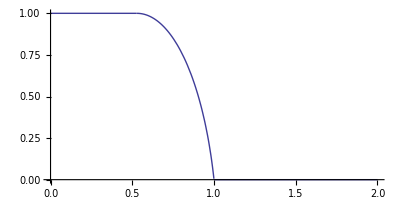

```mathematica
ParametricPlot[{pp2/pp1,Ng},{pp2,1,200000}]
```

```mathematica
qma
```

0.000928855 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
Tp1
```

200

```mathematica
qmp2 =.
```

```mathematica
nmax=100;
qmlist=Array[a1,nmax];
qmdlist=Array[a2,{nmax,2}];
```

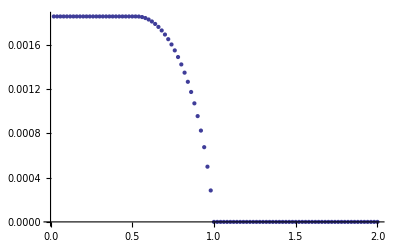

```mathematica
For[i=1,i<nmax+1,i++,
	pp2 = pp1 2 i/nmax;
	qmdlist[[i]]={pp2/pp1,AFa1[pp1,pp2]}
];
ListPlot[qmdlist]
```

```mathematica
eps =.;
kappa =.;
R = .;
cv = .;
Cd = .;
A0=.;
Tp1=.;
Tp2=.;
pp1=.;
pp2=.;
p10=.;
p20=.;
```

```mathematica
keps=.;
Kg=.;
Ndenom=.;
crit=.;
onPositive[x_]=.;
onNegative[x_]=.;
signedSquareL[x_,x0_]=.;
```

### Equations

Calculation of parameters

```mathematica
localExpressions ={
kappa==1+R/cv,
keps==1/(-√eps+√(1+eps)),
Kg==√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1))),
Ndenom==(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1)),
crit==(2/(kappa+1))^(kappa/(kappa-1)),
cp==cv+R
};
```

```mathematica
systemEquationsDA={
qmp2==( onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb),
		dEp1==(onPositive[qmp1e] qmp1e cp Tp2+onNegative[qmp1e]qmp1e cp Tp1+R onPositive[qmp1e] qmp1e Tp2 (1-pp1/pp2)),
		dEp2==(onPositive[qmp2] qmp2 cp Tp1+onNegative[qmp2]qmp2 cp Tp2+R onPositive[qmp2] qmp2 Tp1 (1-pp2/pp1))		
	};
```

```mathematica
systemVariables = {qmp2,dEp1,dEp2,pp1,pp2};
```

### Boundarys

```mathematica
systemBoundaryEquations = { 
pp1 == (cp1 + Zcp1 dEp1 ),
pp2 ==(cp2 + Zcp2 dEp2 )
};
```

```mathematica
systemVariables
```

{qmp2,dEp1,dEp2,pp1,pp2}

### Expressions

The inlet flow is calculated as the outlet flow with reversed sign.

```mathematica
expressions = {
qmp1==-qmp2
};
```

Initial values

```mathematica
cp1/.Solve[systemBoundaryEquations,{cp1,cp2}][[1]]
```

pp1-dEp1 Zcp1

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticOrifice", "displayname" → "PneumaticOrifice"}, {XMLElement["icon", {"isopath" → "PneumaticOrifice.svg", "iconrotation" → "ON", "userpath" → "PneumaticOrifice.svg"}, {}], XMLElement["portpositions", {}, {« 1 »}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "PneumaticOrifice", "displayname" → "PneumaticOrifice"}, {XMLElement["icon", {"isopath" → "PneumaticOrifice.svg", "iconrotation" → "ON", "userpath" → "PneumaticOrifice.svg"}, {}], XMLElement["portpositions", {}, {« 1 »}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "y" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.666667 in "y" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.5 in "x" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

PneumaticOrifice.xml

## T connection

```mathematica
domain="Pneumatic";
displayName="Tconnection";
brief="Pneumatic T-connection";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
inputParameters = {
{Cd,0.65,double,"","Discharge coefficient"},
{R,287.,double,"J/Kg K","Gas constant"},
{cv,718,double,"J/Kg K","heatcoeff"},
{eps,0.02,double,"","Linearisation coeff"}
};
```

qmp1 = qp1;
qmp2 = qp2;

### The system of equations

The flow at inlet and outlet are equal but with oposit sign.

### Equations

Calculation of parameters

```mathematica
nodeConnections = {
PneumaticQnode[1,100000.,"fluid port 1"],
PneumaticQnode[2,100000.,"fluid port 2"],
PneumaticQnode[2,100000.,"fluid port 3"]
};
```

```mathematica
systemEquationsDA = {
qm1+qm2+qm3==0,
dE1+dE2+dE3==0,
dE1==(OnPositive[qm1] qm1 cp T0+OnNegative[qm1]qm1 cp T1),
dE2==(OnPositive[qm2]qm2 cp T0+OnNegative[qm2]qm2 cp T2),
dE3==(OnPositive[qm3]qm3 cp T0+OnNegative[qm3]qm3 cp T3)
};
```

```mathematica
systemVariables = {qm1,dE1,T0,qm2,qm3,p1,dE2,dE3};
```

### Boundaries

```mathematica
systemBoundaryEquations = { 
p1 ==(c1 + Zc1 dE1 ),
p2 ==(c2 + Zc2 dE2 ),
p3 ==(c2 + Zc3 dE3 )
};
```

```mathematica
systemVariables
```

{q1 rhofuel,dE1,T0,qm2,qm3,p1,dE2,dE3}

```mathematica
Compgen[file]
```

General::ivar: q1\ rhofuel is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticTconnection", "displayname" → "PneumaticTconnection"}, {XMLElement["icon", {"isopath" → "PneumaticTconnection.svg", "iconrotation" → "ON", "userpath" → "PneumaticTconnection.svg"}, {}], XMLElement["portpositions", {}, « 1 »]}] in XMLElement["hopsanobjectappearance", {"" … "" → "" … ""}, XMLElement["modelobject", {"typename" → "PneumaticTconnection", "displayname" → "" … ""}, {XMLElement["icon", {"isopath" → "PneumaticTconnection.svg", "iconrotation" → "ON", "userpath" → "PneumaticTconnection.svg"}, {}], XMLElement["portpositions", {}, {« 1 »}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.25 in "y" → 0.25 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.75 in "y" → 0.75 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

PneumaticTconnection.xml

## Q source

```mathematica
domain="Pneumatic";
displayName="Qsrc";
brief="Pneumatic massflow source";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
inputVariables  = {
{qminput,0.,double,"kg/s","mass flow rate"},
{Tinput,273,double,"K","Temperature"}
			};
```

```mathematica
inputParameters = {
{cv,718,double,"","heatcoeff)"}
};
```

```mathematica
portConnections={
PneumaticQports[p1,1.*10^5,"fluid port 1",{0,0.5,270}]
};
```

```mathematica
nodeConnections={
PneumaticQnode[p1,1.*10^5,"fluid port 1"]
};
```

qmp1 = qp1;
qmp2 = qp2;

```mathematica
expressions = {
qmp1==qminput,
dEp1==(onPositive[qmp1] qmp1 cv Tinput + onNegative[qmp1] qmp1 cv Tp1),
pp1==cp1+Zcp1 dEp1
};
```

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"" … "e" → "" … "", « 1 »}, {XMLElement["icon", {"isopath" → "PneumaticQsrc.svg", "iconrotation" → "ON", "userpath" → "PneumaticQsrc.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "0", "name" → "Pp1"}, {}], « 1 », XMLElement["portpose", {« 1 »}, {}]}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "PneumaticQsrc", "displayname" → "PneumaticQsrc"}, {XMLElement["icon", {"isopath" → "PneumaticQsrc.svg", "iconrotation" → "ON", "userpath" → "PneumaticQsrc.svg"}, {}], XMLElement[« 1 »]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "x" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.666667 in "x" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

PneumaticQsrc.xml

## PT source

```mathematica
domain="Pneumatic";
displayName="PTsrc";
brief="Pneumatic pressure and temperature source";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
inputVariables  = {
{pinput,1*10^5,double,"Pa","Input Pressure"},
{Tinput,273.,double,"K","Input Temperature"}
			};
```

```mathematica
nodeConnections={
PneumaticCnode[p1,1.*10^5,"fluid port 1"]
};
```

qmp1 = qp1;
qmp2 = qp2;

```mathematica
expressions = {
		cp1==pinput,
		Tp1==Tinput,
		Zcp1== 0.
			};
```

```mathematica
ka
```

ka

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {« 1 »}, {XMLElement["icon", {"isopath" → "PneumaticPTsrc.svg", "iconrotation" → "ON", "userpath" → "PneumaticPTsrc.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "0", "name" → "Pp1"}, {}], « 10 »[« 1 »], XMLElement["portpose", {« 1 »}, {}]}]}] in XMLElement["hopsanobjectappearance", {"v" … "on" → "" … ""}, XMLElement["modelobject", {"typename" → "PneumaticPTsrc", "displayname" → "PneumaticPTsrc"}, {XMLElement["icon", {"isopath" → "PneumaticPTsrc.svg", "iconrotation" → "ON", "userpath" → "PneumaticPTsrc.svg"}, {}], XMLElement["portpositions", {}, {« 1 »}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "x" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.666667 in "x" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

PneumaticPTsrc.xml

# Partial Components for Pneumatic Systems

## P sensor

```mathematica
domain="Pneumatic";
displayName="Psensor";
brief="Pneumatic pressure sensor";
componentType="ComponentSignal";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
nodeConnections={
PneumaticCnode[p1,1.*10^5,"fluid port 1"]
};
```

```mathematica
outputVariables = {
{psensor,1.*10^5,double,"Pa","Pressure"}
};
```

```mathematica
expressions = {
		psensor==pp1
			};
```

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticPsensor", "displayname" → "P" … "or"}, {XMLElement["icon", {"isopath" → "PneumaticPsensor.svg", "iconrotation" → "ON", "userpath" → "PneumaticPsensor.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pp1"}, {}], XMLElement["portpose", {"x" → "0.5", "y" → "1", "a" → "90", "name" → "Ppsensor"}, {}]}]}] in XMLElement[« 1 »] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

PneumaticPsensor.xml

## T sensor

```mathematica
domain="Pneumatic";
displayName="Tsensor";
brief="Pneumatic tempreature sensor";
componentType="ComponentSignal";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
nodeConnections={
PneumaticCnode[p1,1.*10^5,"fluid port 1"]
};
```

```mathematica
outputVariables = {
{Tsensor,0.,double,"K","Temperature"}
};
```

```mathematica
expressions = {
		Tsensor==Tp1
			};
```

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticTsensor", "" … "" → « 18 »}, {XMLElement["icon", {"isopath" → "PneumaticTsensor.svg", "iconrotation" → "ON", "userpath" → "PneumaticTsensor.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pp1"}, {}], XMLElement["portpose", {"x" → "0.5", "y" → "1", "a" → "90", "name" → "PTsensor"}, {}]}]}] in « 1 » is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

PneumaticTsensor.xml

## Qm sensor

```mathematica
domain="Pneumatic";
displayName="Qmsensor";
brief="Pneumatic massflow sensor";
componentType="ComponentSignal";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
nodeConnections={
PneumaticCnode[p1,1.*10^5,"fluid port 1"]
};
```

```mathematica
outputVariables = {
{qmsensor,0.,double,"kg/s","massflow"}
};
```

```mathematica
expressions = {
		qmsensor==qmp1
			};
```

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticQmsensor", « 1 »}, {XMLElement["icon", {"isopath" → "PneumaticQmsensor.svg", "iconrotation" → "ON", "userpath" → "PneumaticQmsensor.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pp1"}, {}], XMLElement["portpose", {"x" → "0.5", "y" → "1", "a" → "90", "name" → "Pqmsensor"}, {}]}]}] in XMLElement["hopsanobjectappearance", {"" … "" → « 5 »}, XMLElement["modelobject", {"typename" → "PneumaticQmsensor", "" … "" → "" … ""}, {XMLElement["icon", {"isopath" → "PneumaticQmsensor.svg", "iconrotation" → "ON", "userpath" → "PneumaticQmsensor.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pp1"}, {}], XMLElement["portpose", « 1 », {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

PneumaticQmsensor.xml

## dE sensor

```mathematica
domain="Pneumatic";
displayName="dEsensor";
brief="Pneumatic energy flow sensor";
componentType="ComponentSignal";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
nodeConnections={
PneumaticCnode[p1,1.*10^5,"fluid port 1"]
};
```

```mathematica
outputVariables = {
{dEsensor,0.,double,"J/s","energy flow"}
};
```

```mathematica
expressions = {
		dEsensor==dEp1
			};
```

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticdEsensor", « 1 »}, {XMLElement["icon", {"isopath" → "PneumaticdEsensor.svg", "iconrotation" → "ON", "userpath" → "PneumaticdEsensor.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pp1"}, {}], XMLElement["portpose", {"x" → "0.5", "y" → "1", "a" → "90", "name" → "PdEsensor"}, {}]}]}] in XMLElement["hopsanobjectappearance", {"" … "" → « 5 »}, XMLElement["modelobject", {"typename" → "PneumaticdEsensor", "" … "" → "" … ""}, {XMLElement["icon", {"isopath" → "PneumaticdEsensor.svg", "iconrotation" → "ON", "userpath" → "PneumaticdEsensor.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pp1"}, {}], XMLElement["portpose", « 1 », {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

PneumaticdEsensor.xml